```mathematica
RepFunc[f_,reps_]:=If[reps==0,#&,f[RepFunc[f,reps-1][#]]&];
ToPlane[cpnts_]:=cpnts/.(c_/;NumberQ[c]):>{Re[c],Im[c]};
ExpFixPoint=RepFunc[Log,200][1.1];
ExpFixPointNeg = Conjugate[ExpFixPoint];
```

```mathematica
PlotComplexAbsArg[f_,rng_]:=Module[{rmin,imin,rmax,imax},
{rmin,imin,rmax,imax}=rng/.{Complex[rmin_,imin_],Complex[rmax_,imax_]}->{rmin,imin,rmax,imax};
GraphicsRow[{
DensityPlot[Abs[f[x+y I]],{x,rmin,rmax},{y,imin,imax},PlotLabel->"Abs",ColorFunction->"TemperatureMap"],
DensityPlot[Arg[f[x+y I]],{x,rmin,rmax},{y,imin,imax},PlotLabel->"Arg",ColorFunction->"TemperatureMap"]
}]
];

PlotComplexReIm[f_,rng_,args___]:=Module[{rmin,imin,rmax,imax},
{rmin,imin,rmax,imax}=rng/.{Complex[rmin_,imin_],Complex[rmax_,imax_]}->{rmin,imin,rmax,imax};
GraphicsRow[{
DensityPlot[Re[f[x+y I]],{x,rmin,rmax},{y,imin,imax},PlotLabel->"Re",ColorFunction->"TemperatureMap",args],
DensityPlot[Im[f[x+y I]],{x,rmin,rmax},{y,imin,imax},PlotLabel->"Im",ColorFunction->"TemperatureMap",args]
}]
];

PlotComplexRe[f_,rng_]:=Module[{rmin,imin,rmax,imax},
{rmin,imin,rmax,imax}=rng/.{Complex[rmin_,imin_],Complex[rmax_,imax_]}->{rmin,imin,rmax,imax};
DensityPlot[Re[f[x+y I]],{x,rmin,rmax},{y,imin,imax},PlotLabel->"Re",ColorFunction->"TemperatureMap"]
];

ListPlotComplex[pnts_,args___]:=ListPlot[{Re[#],Im[#]}&/@pnts, args];
CPnts[pnts_]:={Re[#],Im[#]}&/@pnts;
```

```mathematica
rinner=0.0001;
maxiters=50;

XiItersRec[x_,iter_]:=
If[iter>maxiters,Infinity,
If[Abs[x-ExpFixPoint]≤rinner,
iter,
XiItersRec[Log[x],iter+1]
]];
XiIters[x_]:=XiItersRec[x,0];

XiRec[x_,iter_]:=
If[iter>maxiters,Infinity,
If[Abs[x-ExpFixPoint]≤rinner,
x-ExpFixPoint,
ExpFixPoint*XiRec[Log[x],iter+1]]];
Xi[x_]:=XiRec[x,0];

XiNegRec[x_,iter_]:=
If[iter>maxiters,Infinity,
If[Abs[x-ExpFixPointNeg]≤rinner,
x-ExpFixPointNeg,
ExpFixPointNeg*XiNegRec[Log[x],iter+1]]];
XiNeg[x_]:=XiNegRec[x,0];

XiFull[x_]:=If[Im[x]≥0,Xi[x],XiNeg[x]];

XiInvIter[xi_,iter_]:=RepFunc[Exp,iter][ExpFixPoint^(-iter) *xi+ExpFixPoint];
XiInv[xi_]:=Module[{iter,x},
For[iter=0,iter≤maxiters,iter++,
If[Abs[ExpFixPoint^(-iter)*xi]≤rinner,Return[XiInvIter[xi,iter]]];
];
Infinity
];

XiInvNegIter[xi_,iter_]:=RepFunc[Exp,iter][ExpFixPointNeg^(-iter) *xi+ExpFixPointNeg];
XiInvNeg[xi_]:=Module[{iter,x},
For[iter=0,iter≤maxiters,iter++,
If[Abs[ExpFixPointNeg^(-iter)*xi]≤rinner,Return[XiInvNegIter[xi,iter]]];
];
Infinity
];


XiItersFromXi[xi_]:=Module[{iter,x},
For[iter=0,iter≤maxiters,iter++,
If[Abs[ExpFixPoint^(-iter)*xi]≤rinner,Return[iter]];
];
Infinity
];

FracExp[x_,n_]:=XiInv[ExpFixPoint^n *Xi[x]];
FracExpFull[x_,n_]:=
If[Im[x]≥0,
XiInv[ExpFixPoint^n *Xi[x]],
XiInvNeg[ExpFixPointNeg^n *XiNeg[x]]
];
FracExpFullNull[x_,n_]:=Module[{val=FracExpFull[x,n]},
If[val==Infinity,FracExpFull[x+0.0001*(1+I),n],val]
];



Psi[z_]:=Log[Xi[z]];
PsiInv[psi_]:=XiInv[Exp[psi]];

AbelExp[x_,n_]:=PsiInv[Psi[x]+ExpFixPoint*n];
```

```mathematica
FracExpFullNull[0.0,0.1]
```

-0.000457523+0.000117019 ⅈ

```mathematica
testInp=ExpFixPoint+15;
Xi[testInp]
XiIters[testInp]
XiInvIter[Xi[testInp],XiIters[testInp]]
XiInv[Xi[testInp]]
testInp
```

-0.997925+6.38778 ⅈ

35

15.3181+1.33724 ⅈ

15.3181+1.33724 ⅈ

15.3181+1.33724 ⅈ

```mathematica
XiIters[1.02]
```

34

```mathematica
Needs["NumericalCalculus`"];
ND[Xi[x],x,ExpFixPoint]
```

1.00005+0.000203407 ⅈ

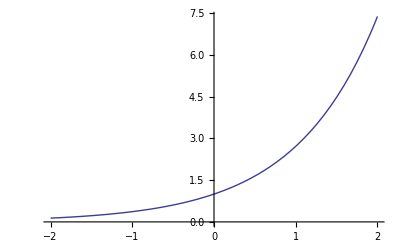

```mathematica
Plot[{Exp[x]},{x,-2,2}]
```

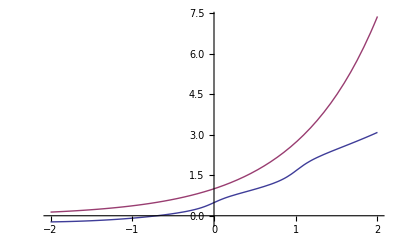

```mathematica
Plot[{Re[FracExp[x+0.2I,0.5]],Exp[x]},{x,-2,2}]
```

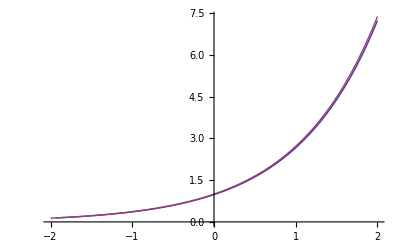

```mathematica
Plot[{Re[FracExp[FracExp[x+0.2I,0.5],0.5]],Exp[x]},{x,-2,2}]
```

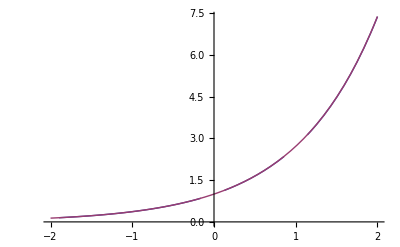

```mathematica
Plot[{Re[FracExp[FracExp[x+0.05I,0.5],0.5]],Exp[x]},{x,-2,2}]
```

```mathematica
Plot[{Re[AbelExp[AbelExp[x+0.05I,0.5],0.5]],Exp[x]},{x,-2,2}]
```

-Graphics-

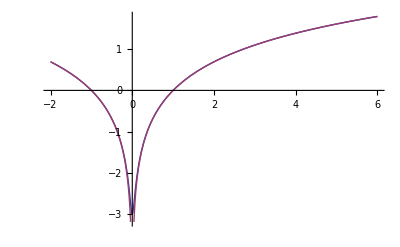

```mathematica
Plot[{Re[FracExp[x+0.05I,-1]], Re[Log[x]]},{x,-2,6}]
```

```mathematica
Manipulate[Plot[{Re[FracExp[x+0.05I,n]]},{x,-2,2}],{{n,0.5},-3,3}]
```

```mathematica
Manipulate[Plot[{Re[AbelExp[x+0.05I,n]]},{x,-2,2}],{{n,0.5},-3,3}]
```

```mathematica
Manipulate[Plot[{Re[FracExpFull[x+0.01I,n]],Im[FracExpFull[x+0.01I,n]]},{x,-2,2}],{{n,-0.34},-3,3}]
```

```mathematica
Manipulate[Plot[{Re[FracExp[x+0.2I,n+I n]]},{x,-2,2}],{{n,0},-3,3}]
```

```mathematica
ExpFixPoint*(Log[testInp]-ExpFixPoint)
```

2.43995+2.83131 ⅈ

```mathematica
Xirec2[x_,iter_]:=
If[iter>maxiters,Infinity,
If[Abs[x-ExpFixPoint]≤rinner,
ExpFixPoint^iter (x-ExpFixPoint),
If[Abs[x-ExpFixPointNeg]≤rinner,
ExpFixPointNeg^iter (x-ExpFixPointNeg),
Xirec2[Log[x],iter+1]
]]];
Xi2[x_]:=Xirec2[x,0];
```

```mathematica
testInp=ExpFixPoint+0.1
Xi[testInp]
Xi2[testInp]
XiIters[testInp]
XiInvIter
XiItersFromXi[Xi[testInp]]
```

0.418132+1.33724 ⅈ

0.10142+0.00304518 ⅈ

0.10142+0.00304518 ⅈ

22

XiInvIter

22

```mathematica
XiInvIter[Xi[testInp],8]
```

0.417878+1.33728 ⅈ

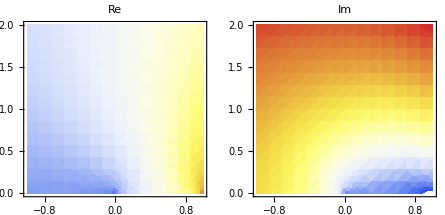

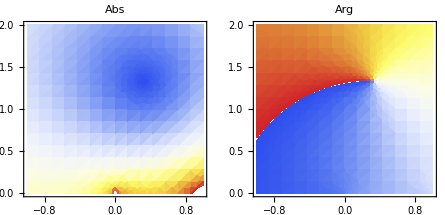

```mathematica
plotRng={-1+0.00001I,1+2I};
PlotComplexReIm[Xi,plotRng]
PlotComplexAbsArg[Xi,plotRng]
```

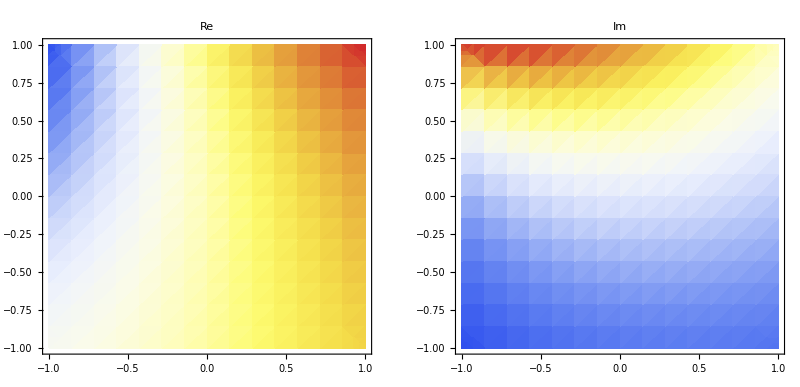

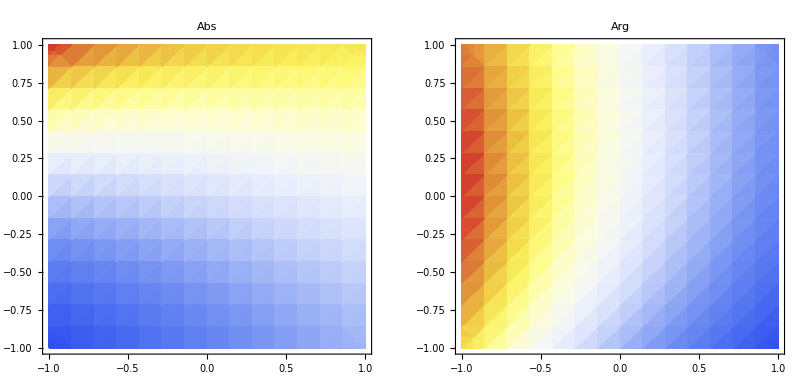

```mathematica
plotRng={-1-1I,1+1I};
PlotComplexReIm[XiInv,plotRng]
PlotComplexAbsArg[XiInv,plotRng]
```

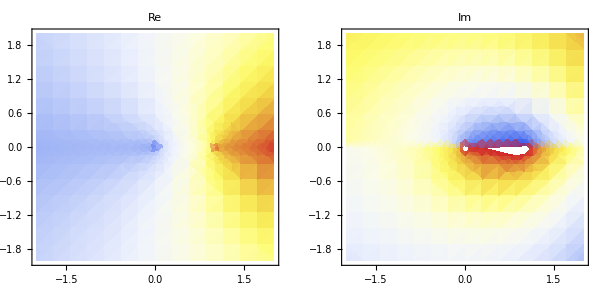

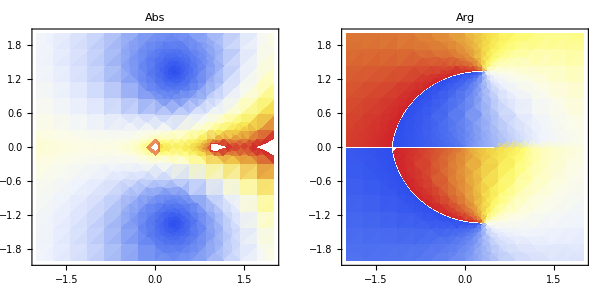

```mathematica
plotRng={-2-2I,2+2I};
PlotComplexReIm[XiFull,plotRng]
PlotComplexAbsArg[XiFull,plotRng]
```

```mathematica
ComplexInterpolation[pnts_]:=Module[{rpnts,ipfunc},
rpnts=pnts/.{pnt_?NumberQ,val_}->{{Re[pnt],Im[pnt]},val};
ipfunc=Interpolation[rpnts,InterpolationOrder->1];
ipfunc[Re[#],Im[#]]&
];
```

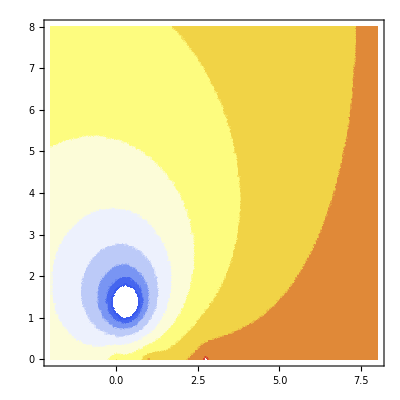

```mathematica
DensityPlot[Re[XiIters[x+y I]],{x,-2,8},{y,0,8},ColorFunction->"TemperatureMap",PlotPoints->100]
```

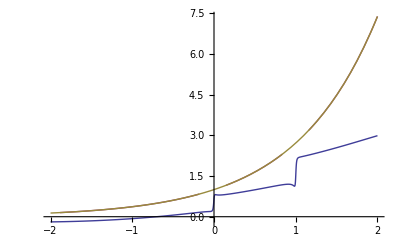

```mathematica
Plot[{Re[FracExp[x+0.01I,0.5]],Re[FracExp[FracExp[x+0.01I,0.5],0.5]],Exp[x]},{x,-2,2}]
```

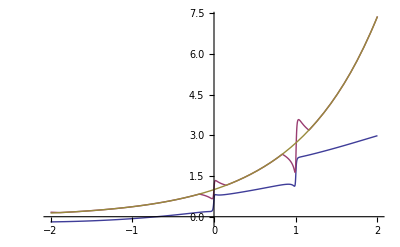

```mathematica
Plot[{Re[FracExpFull[x+0.01I,0.5]],Re[FracExpFull[FracExpFull[x+0.01I,0.5],0.5]],Exp[x]},{x,-2,2}]
```

```mathematica
XiIters[1+0.01I]
```

34

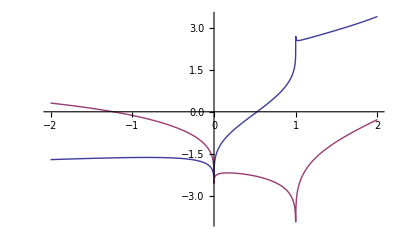

```mathematica
Plot[{Re[Xi[x]],Im[Xi[x]]},{x,-2,2}]
```

```mathematica
Xi[1+0.01I]
Xi[1+0.01I]*ExpFixPoint^0.5
XiInv[Xi[1+0.01I]*ExpFixPoint^0.5]
```

2.0924-3.19999 ⅈ

4.25064-1.42318 ⅈ

1.50246-1.18851 ⅈ

```mathematica
ExpFixPoint^0.5
```

0.91997+0.726782 ⅈ

```mathematica
ExpFixPoint
```

0.318132+1.33724 ⅈ

```mathematica
Xi[1.502455602250734+1.1885050995151523 ⅈ]
```

1.32703+0.334687 ⅈ

```mathematica
XiItersFromXi[Xi[1+0.01I]*ExpFixPoint^0.5]
```

34

```mathematica
iter=35;
Abs[ExpFixPoint^(-iter)*(Xi[1+0.01I]*ExpFixPoint^0.5)]
```

0.000065438

```mathematica
XiInvIter[(Xi[1+0.01I]*ExpFixPoint^0.5),60]
```

1.50263-1.18833 ⅈ

```mathematica
targetXi=Xi[1+0.01I]*ExpFixPoint^0.5;
targetXi=Xi[1+0.3I];
NSolve[Xi[x]==targetXi,x]
```

NSolve[If[Abs[(-0.318132-1.33724 ⅈ)+x]≤0.0001,x-ExpFixPoint,ExpFixPoint XiRec[Log[x],0+1]]==1.4059-1.55023 ⅈ,x]

```mathematica
Xi[ExpFixPoint+0.1]
```

0.10142+0.00304518 ⅈ

```mathematica
Xi[1.2]
```

2.66066-1.77724 ⅈ

```mathematica
targetXi=Xi[0.5+0.5I];
```

```mathematica
targetXi=Xi[1+0.01I]*ExpFixPoint^0.5
```

4.25064-1.42318 ⅈ

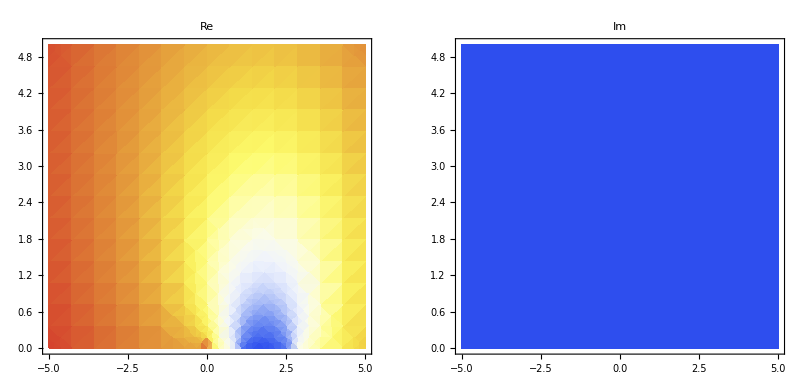

```mathematica
PlotComplexReIm[Abs[Xi[#]-targetXi]&,{-5+0.0001I,5+5I}]
```

```mathematica
targetXi
Xi[2]
```

4.25064-1.42318 ⅈ

3.40247-0.275937 ⅈ

```mathematica
targetXi=Xi[1+0.01I]*ExpFixPoint^0.5
```

4.25064-1.42318 ⅈ

```mathematica
plotRng={3-2I,5+2I};
PlotComplexReImWithLegends[XiInv,plotRng]
```

PlotComplexReImWithLegends[XiInv,{3-2 ⅈ,5+2 ⅈ}]

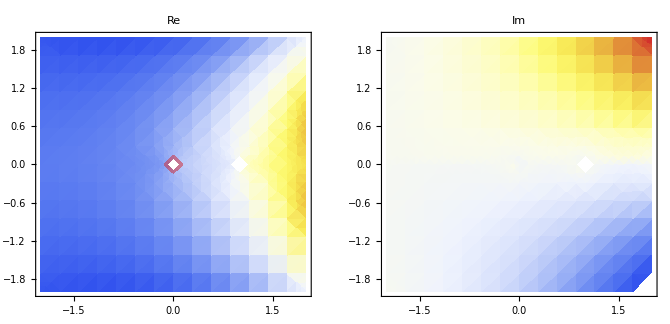

```mathematica
PlotComplexReIm[FracExpFullNull[#,0.6]&,{-2-2I,2+2I},PlotRange->Automatic]
```

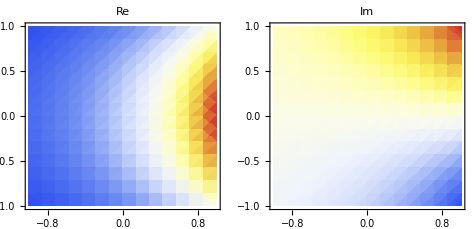

```mathematica
PlotComplexReIm[Exp[#]&,{-1-1I,1+1I},PlotRange->Full]
```

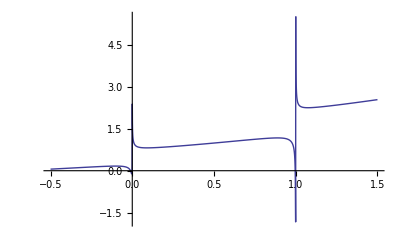

```mathematica
Plot[Re[FracExpFullNull[x,0.5]],{x,-0.5,1.5}]
```

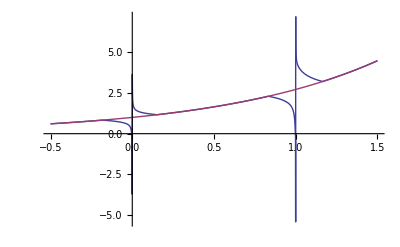

```mathematica
Plot[{Re[FracExpFullNull[FracExpFullNull[x,0.5],0.5]],Exp[x]},{x,-0.5,1.5}]
```

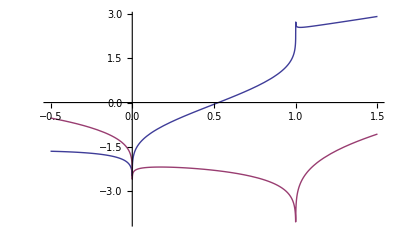

```mathematica
Plot[{Re[Xi[x]],Im[Xi[x]]},{x,-0.5,1.5}]
```

```mathematica
Xi[1]
```

(0.608984-0.793183 ⅈ) ∞

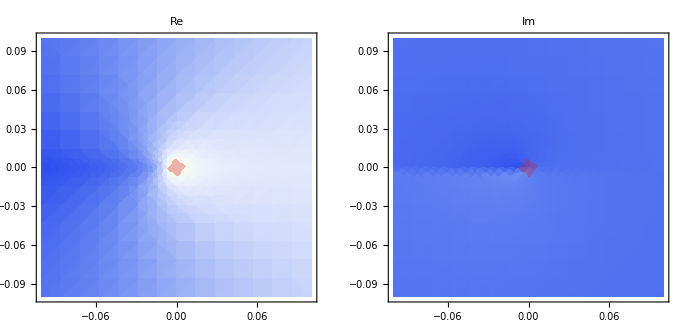

```mathematica
PlotComplexReIm[FracExpFullNull[#,0.6]&,{-0.1(1+I),0.1(1+I)},PlotRange->Full]
```

```mathematica
dx=0.1;
c=ExpFixPoint;a=Re[ExpFixPoint];
U0=Table[a+y I,{y,0,Im[c],dx}];
U1=Exp[U0];
B0=Table[x,{x,a,Abs[c], dx}];
(*U1=Table[Abs[c]Exp[I ϕ],{ϕ,0,Arg[c],dx}];
B0ss=Table[x,{x,a,1,dx}];
B1s=Table[x,{x,1,Abs[c],dx}];*)
NL=Table[x+I Im[c],{x,a,-3,-dx}];
Basefig=Join[U0,U1,B0];
Fullfig=Join[U0, U1, B0,Exp[U1],Log[U0],Log[B0],Exp[B0]];
Fullfig=Join[Basefig, Exp[Basefig], Log[Basefig]];
```

```mathematica
ListPlot[CPnts[Basefig],AspectRatio->Automatic]
```

-Graphics-

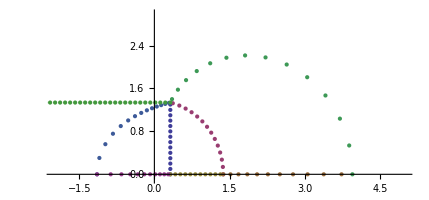

```mathematica
ListPlot[{CPnts[U0], CPnts[U1], CPnts[B0],CPnts[Exp[U1]],CPnts[Log[U0]],CPnts[Log[B0]],CPnts[Exp[B0]],CPnts[NL]},PlotRange->{{-2,5},{-0.1,3}},AspectRatio->Automatic]
```

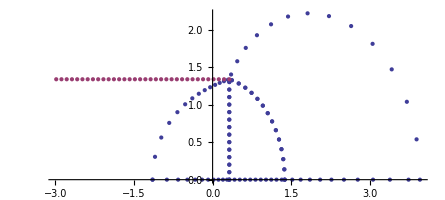

```mathematica
ListPlot[{CPnts[Fullfig],CPnts[NL]},AspectRatio->Automatic]
```

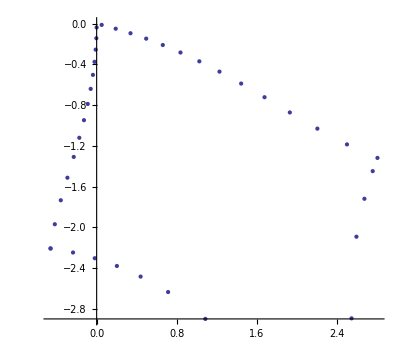

```mathematica
ListPlot[CPnts[Xi/@Basefig] ,AspectRatio->Automatic]
```

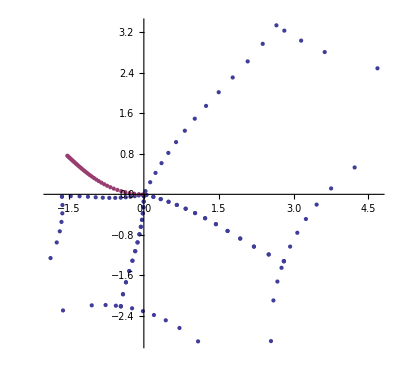

```mathematica
ListPlot[{CPnts[Xi/@Fullfig],CPnts[Xi/@NL]} ,AspectRatio->Automatic]
```

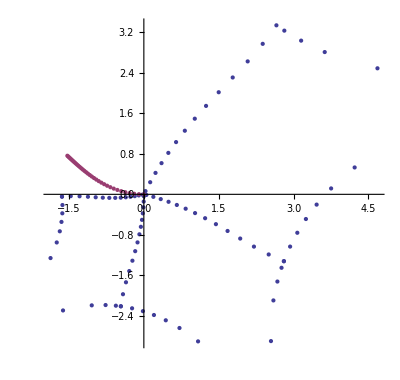

-Graphics-

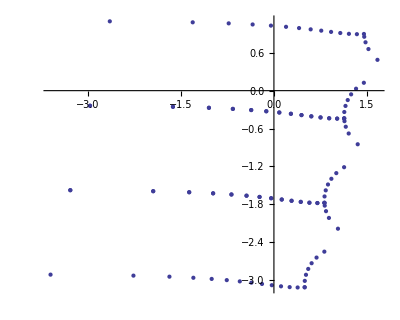

```mathematica
ListPlot[{CPnts[(Log[Xi[#]]&)/@Fullfig]} ,AspectRatio->Automatic]
```

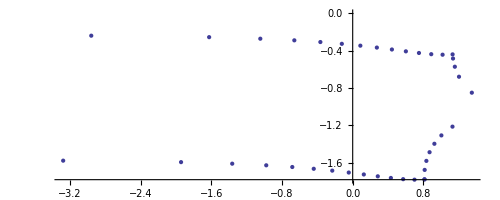

```mathematica
ListPlot[{CPnts[(Log[Xi[#]]&)/@Basefig]} ,AspectRatio->Automatic]
```

## Codomain of ξ

```mathematica
XiRec[x_,iter_]:=
If[iter>maxiters,Infinity,
If[Abs[x-ExpFixPoint]≤rinner,
x-ExpFixPoint,
ExpFixPoint*XiRec[Log[x],iter+1]]];
Xi[x_]:=XiRec[x,0];
```

```mathematica
CCirc[r_,n_]:=Array[r Exp[I #]&,n,{0,2π}];
CP=ExpFixPoint;
IC=CCirc[0.1,50];
IC2=CCirc[0.2,50];
CIC=CP+IC;
CIC2=CP+IC2;
```

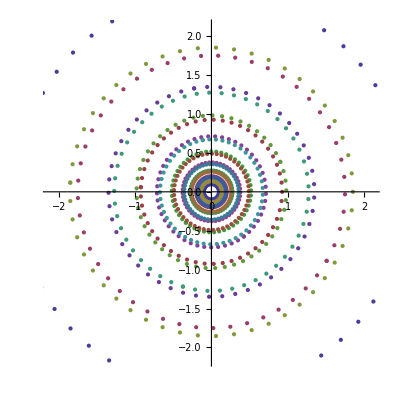

```mathematica
AllP={};
For[i=0,i<10,i++,
AllP=Join[AllP, {CP^i IC,CP^i IC2}]]
ListPlot[CPnts/@AllP, AspectRatio->Automatic]
```

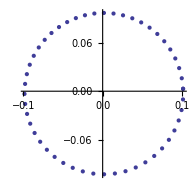

```mathematica
ListPlot[CPnts[Xi/@CIC],AspectRatio->Automatic]
```

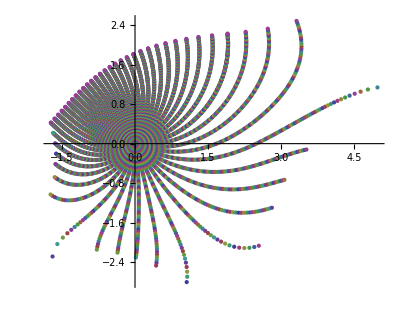

```mathematica
AllP={};
For[r=0.01,r<3,r+=0.02,
AllP=Join[AllP, {Xi/@(CP+CCirc[r,50])}]]
ListPlot[CPnts/@AllP, AspectRatio->Automatic]
```